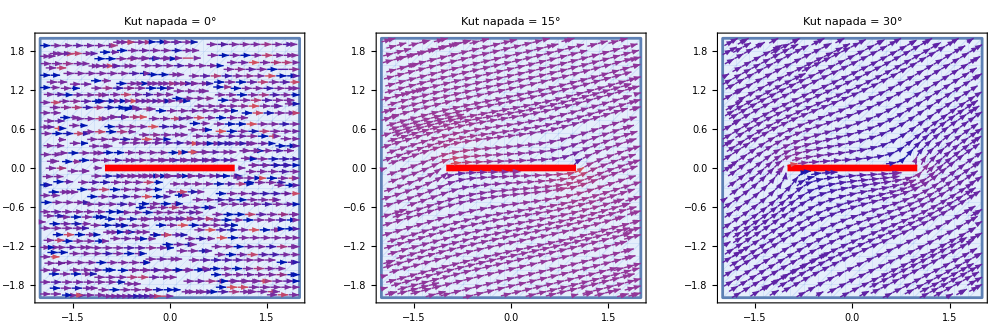

```mathematica
(*Definiranje vizualnog stila iz p01,p02 i p03*)baseOptions={Frame->True,Axes->False,FrameStyle->Black,Background->White,ImageSize->400,(*Smanjeno za GraphicsGrid,original je 800*)PlotRange->{{-2,2},{-2,2}}};

(*1. Inverz Joukowskog:Mapira ravninu ploče natrag na krug*)
toKrug[zeta_]:=zeta+Sqrt[zeta-1] Sqrt[zeta+1];

(*2. Potencijal za kosi tok oko kruga pod kutom phi*)
Wkrug[z_,phi_]:=z*Exp[-I phi]+1/(z*Exp[-I phi]);

(*3. Kompleksna brzina u ravnini ploče*)
ComplexVelocity[zeta_,phi_]:=Module[{z},z=toKrug[zeta];
Conjugate[(Exp[-I phi]-Exp[I phi]/z^2)/(1-1/z^2)]];

(*Kutovi napada*)
angles={0,15 Degree,30 Degree};

plots=Table[StreamPlot[{Re[ComplexVelocity[x+I y,phi]],Im[ComplexVelocity[x+I y,phi]]},{x,-2,2},{y,-2,2},(*Stil strelica preuzet iz datoteka p01,p02,p03*)StreamStyle->Directive[Black,Arrowheads[0.02]],StreamPoints->Fine,StreamScale->{Small,Scaled[0.6],None},RegionFunction->Function[{x,y},Not[Abs[y]<0.03&&Abs[x]<1.05]],AspectRatio->Automatic,PlotLabel->Style[Row[{"Kut napada = ",phi/Degree,"°"}],Black,14],(*Crvena ploča ostaje vodoravna,ali stilski usklađena*)Epilog->{Red,Thickness[0.012],Line[{{-1,0},{1,0}}]},Evaluate@baseOptions],{phi,angles}];

(*Prikaz u mreži s bijelom pozadinom*)
GraphicsGrid[{plots},Background->White,ImageSize->1000]
```